{a→0.272672,b→1.68448,c→0.254294}

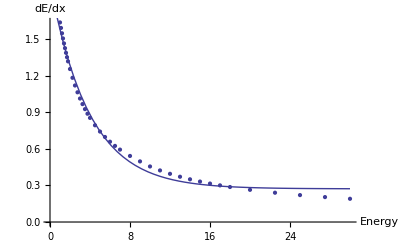

0.27267185723475307 + 1.6844812118388253/Power(E,0.2542936852380424*x)

```mathematica
HeliumDat=Import["~/nuclear/be9/summed/SRIM/Helium in Beryllium parsed.dat"];
Length[HeliumDat[[All,1]]];
HeliumList=Transpose[{HeliumDat[[All,1]],HeliumDat[[All,3]]+HeliumDat[[All,4]]}];
LP=ListPlot[HeliumList,AxesLabel->{Energy,dE/dx}];
form=a+b*ⅇ^(-c*x);
fit1=FindFit[HeliumList,form,{a,b,c},x]
Plot[form/.fit1,{x,0,30},PlotRange->Full];
Show[LP,%]
Export["~/nuclear/be9/summed/SRIM/AlphaFit.png",%];
CForm[form/.fit1]
```

{{4.5,4.46486},{5.,4.39044},{5.5,4.30909},{6.,4.22279},{6.5,4.13454},{7.,4.04632},{8.,3.87295},{9.,3.70866},{10.,3.55343},{11.,3.40923},{12.,3.27407},{13.,3.14993},{14.,3.03281},{15.,2.9247},{16.,2.82461},{17.,2.73052},{18.,2.64245},{20.,2.48232},{22.5,2.30819},{25.,2.15908},{27.5,2.01299},{30.,1.87692}}

{a→1.20597,b→4.33922,c→0.0613897}

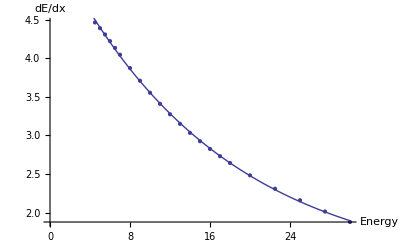

1.205966255137941 + 4.339223452110011/Power(E,0.06138967944782508*x)

```mathematica
ClearAll["Global*'"]
BerylliumDat=Import["~/nuclear/be9/summed/SRIM/Beryllium in Beryllium parsed.dat"];
BerylliumList=Transpose[{BerylliumDat[[All,1]],BerylliumDat[[All,3]]+BerylliumDat[[All,4]]}];
BerylliumList=Drop[BerylliumList,18]
LP=ListPlot[BerylliumList,AxesLabel->{Energy,dE/dx}];
form=a+b*ⅇ^(-c*x);
fit1=FindFit[BerylliumList,form,{a,b,c},x]
Plot[form/.fit1,{x,0,30},PlotRange->Full];
Show[LP,%]
Export["~/nuclear/be9/summed/SRIM/BerylliumFit.png",%];
CForm[form/.fit1]
```